```mathematica
xmin = (L^2+R^2-(c t)^2)/(2*R*L), tmin = (R-L)/c, tcut = (L+R)/c;
```

```mathematica
Result = Integrate[2π R^2 Exp[Sqrt[R^2+L^2-2 R L x ]/(c τ)](R - L x)/(4 π  Sqrt[R^2+L^2-2 R L x]^3) ,{x,xmin,1},Assumptions->{R>0,L>0,L<R,L+c t>R,c>0,t>0}]
```

(ⅇ^(-L/(c τ)) (τ (-c ⅇ^(R/(c τ)) t (-L-R+c τ)+ⅇ^((L+c t)/(c τ)) (L^2-R^2+c^2 t τ))+ⅇ^(L/(c τ)) (L^2-R^2) t ExpIntegralEi[(-L+R)/(c τ)]-ⅇ^(L/(c τ)) (L^2-R^2) t ExpIntegralEi[t/τ]))/(4 c L t τ)

```mathematica
f[L_, R_, c_, τ_, t_] = 1/τ Exp[-t/τ]Piecewise[{{0,t<tmin},{Result, t<tcut},{Result /. t->tcut, t≥tcut}}];
```

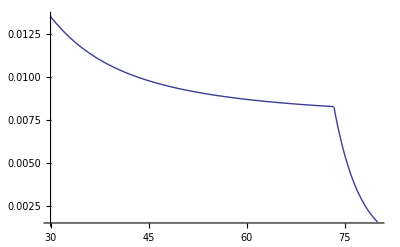

```mathematica
Plot[f[10000.0,12000,300,4,t], {t,30,80}, PlotRange->All]
```

```mathematica
ResultSeries1 = FullSimplify[Result /. ExpIntegralEi[(-L+R)/(c τ)] -> (Normal[Series[ExpIntegralEi[x],{x,Infinity,1}]] /. x->(-L+R)/(c τ))/. ExpIntegralEi[t/τ] -> (Normal[Series[ExpIntegralEi[x],{x,Infinity,1}]] /. x->t/τ)]
```

(c (-ⅇ^((-L+R)/(c τ))+ⅇ^(t/τ)) τ)/(4 L)

```mathematica
ResultSeries2 = FullSimplify[Result1 /. ExpIntegralEi[(-L+R)/(c τ)] -> (Normal[Series[ExpIntegralEi[x],{x,Infinity,2}]] /. x->(-L+R)/(c τ))/. ExpIntegralEi[t/τ] -> (Normal[Series[ExpIntegralEi[x],{x,Infinity,2}]] /. x->t/τ)]
```

(((2 c^2 ⅇ^((-L+R)/(c τ)) R)/(L-R)+(ⅇ^(t/τ) (-L^2+R^2+c^2 t^2))/t^2) τ)/(4 c L)

```mathematica
cdf1Series1 = FullSimplify[Integrate[1/τ Exp[-t/τ]ResultSeries1,{t,tmin,x},Assumptions->{R>0,L>0,t>0,L<R,x>tmin,c>0}]]
```

(L-R+c (x+(-1+ⅇ^(-(L-R+c x)/(c τ))) τ))/(4 L)

```mathematica
FullSimplify[cdf1Series1 /. x-> tcut,Assumptions->{L>0,R>0}]
```

(2 L+c (-1+ⅇ^(-(2 L)/(c τ))) τ)/(4 L)

```mathematica
cdf1Series2 =FullSimplify[Integrate[1/τ Exp[-t/τ]ResultSeries2,{t,tmin,x},Assumptions->{R>0,L>0,t>0,L<R,x>tmin,c>0}]]
```

(L^3-L^2 (R-2 c x)-L (R^2+2 c R x-c^2 x^2)+R (R^2+c^2 x (-x+2 τ-2 ⅇ^(-(L-R+c x)/(c τ)) τ)))/(4 c L (L-R) x)

```mathematica
FullSimplify[cdf1Series2 /. x-> tcut,Assumptions->{L>0,R>0}]
```

(2 L^2-2 L R+c R τ-c ⅇ^(-(2 L)/(c τ)) R τ)/(2 L^2-2 L R)

```mathematica
cdf2Series1 = Simplify[Integrate[1/τ Exp[-t/τ](ResultSeries1/.t->tcut),{t,tcut,x},Assumptions->{R>0,L>0,t>0,L<R,x>tcut,c>0}]]
```

(c ⅇ^(-(2 L+c x)/(c τ)) (-1+ⅇ^((2 L)/(c τ))) (-ⅇ^((L+R)/(c τ))+ⅇ^(x/τ)) τ)/(4 L)

```mathematica
cdf2Series2 = Simplify[Integrate[1/τ Exp[-t/τ](ResultSeries2/.t->tcut),{t,tcut,x},Assumptions->{R>0,L>0,t>0,L<R,x>tcut,c>0}]]
```

-(c ⅇ^(-(2 L+c x)/(c τ)) (ⅇ^((L+R)/(c τ))-ⅇ^(x/τ)) R (L+ⅇ^((2 L)/(c τ)) (L-R)+R) τ)/(2 L (L-R) (L+R))